```mathematica
(* Available Plays:
1. Antigone
2. Death of a Salesman
3-22. Hamlet
23-48. King Lear
49-57. Midsummer Night's Dream
58. Oedipus At Colonus
59. Oedipus The King
60-83. Romeo and Juliet
84. The Glass Menagerie
85-93 The Tempest *)
(* play#, negativitybias, positive tolerance, negative tolerance, startInd, endInd *)
plays={"Antigone", "Death of a Salesman", "Hamlet", "King Lear", "Midsummer Night's Dream", "Oedipus At Colonus", "Oedipus The King", "Romeo and Juliet", "The Tempest", "The Glass Menagerie"};
playConditions=Table[plays⟦i⟧->{i,1,.30,-.30},{i,1,Length[plays]}];
exceptions={
Values[playConditions⟦1⟧]->{1,1.2,.20,-.30},
Values[playConditions⟦2⟧]->{2,1.35,.30,-.20},
Values[playConditions⟦3⟧]->{3,1.25,.40,-.30},
Values[playConditions⟦4⟧]->{4,1.3,.30,-.30},
Values[playConditions⟦5⟧]->{5,1.3,.30,-.30},
Values[playConditions⟦6⟧]->{6,1.3,.30,-.30},
Values[playConditions⟦7⟧]->{7,1.3,.30,-.30},
Values[playConditions⟦8⟧]->{8,1.3,.35,-.30},
Values[playConditions⟦9⟧]->{9,1.5,.20,-.20},
Values[playConditions⟦10⟧]->{10,1.2,.30,-.30}};
playConditions=playConditions/.exceptions;
playNum=9;
```

```mathematica
(* Process Plays *)
SetDirectory[NotebookDirectory[]];
files=FileNames["*.txt",NotebookDirectory[]];
text=StringJoin[Import[#]&/@files⟦84;;84⟧];
speakerOrder=Capitalize[ToLowerCase@StringCases[text,Shortest["<b>"~~x__~~"</b>"]->x]//Flatten,"AllWords"];
nameList=speakerOrder//DeleteDuplicates;
```

```mathematica
(* Separates lines of text ready for sentiment analysis *)
lines=StringSplit[text//StringDelete[Shortest["<i>"~~x__~~"</i>"]]//StringDelete[Shortest["["~~x__~~"]"]],Shortest["<b>"~~x__~~"</b>"]]//StringDelete[Shortest["<"~~x___~~">"]]//Rest;
sentences=lines//TextSentences;
lineLength=Length/@sentences;
```

```mathematica
(* Create directed edges for graph *)
speakerBySentence=Table[Table[speakerOrder⟦i⟧,Length[sentences⟦i⟧]],{i,1,Length[lines]}]//Flatten;
recipientByLine=Prepend[Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}],Table[speakerOrder⟦2⟧,Length[First[sentences]]]];
recipientBySentence=Nest[Prepend[speakerOrder⟦2⟧],Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}]//Flatten,Length[First[sentences]]];

emphasis=WordFrequency[Flatten[sentences],#,IgnoreCase->True]&/@nameList;
diffRecipientPos=SortBy[Position[emphasis,_?Positive],Last];

brokenInd=TakeList[Range[Length[recipientBySentence]],lineLength];
sentenceToLineRules=Table[i->First@@Position[brokenInd,i],{i,1,Length[recipientBySentence]}];
lineIndOfSentences=Range[Length[recipientBySentence]]/.sentenceToLineRules;
sentenceNumOfDiffLine[x_]:=Last@diffRecipientPos⟦x⟧-Total[lineLength⟦;;lineIndOfSentences⟦Last@diffRecipientPos⟦x⟧⟧-1⟧];

For[i=1,i≤Length[diffRecipientPos],i++,
recipientByLine⟦lineIndOfSentences⟦Last@diffRecipientPos⟦i⟧⟧,sentenceNumOfDiffLine[i];;⟧=nameList⟦First@diffRecipientPos⟦i⟧⟧]

recipientBySentence=recipientByLine//Flatten;
finalRules=Table[speakerBySentence⟦i⟧->recipientBySentence⟦i⟧,{i,1,Length[speakerBySentence]}];
ruleList=DeleteCases[DeleteDuplicates[finalRules],x_->x_];
```

```mathematica
(* Implement Sentiment Analysis of lines *)
feelings=Classify["Sentiment",#,"Probabilities"]&/@sentences//Flatten;
```

```mathematica
(* Put sentiment into edges *)
{pos,neu,neg}=Table[feelings⟦i⟧[#],{i,1,Length[feelings]}]&/@{"Positive","Neutral","Negative"};
negBias=Values[playConditions]⟦playNum⟧⟦2⟧;
Health=(pos-negBias*neg)/(1+neu);
sentenceHealth={finalRules⟦#⟧,Health⟦#⟧}&/@Range[Length[Health]];
sentenceHealthFormat=Cases[sentenceHealth,{#,_}]&/@ruleList;
relationshipHealth=Table[Mean[Table[sentenceHealthFormat⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sentenceHealthFormat⟦i⟧]}]],{i,1,Length[sentenceHealthFormat]}];
```

```mathematica
(* Incorporate Frequency for into Health *)
freq=Table[Length[sentenceHealthFormat⟦i⟧],{i,1,Length[sentenceHealthFormat]}];
freqMultiplier[x_]:=(Log[x]+2)/2;
thickness=N[freq]/Max[N[freq]]*.012;
edgeWidth=Table[ruleList⟦i⟧->freqMultiplier[N[freq⟦i⟧]],{i,Length[ruleList]}];
```

```mathematica
(* Exclude Neutral/Conflicted Relationships *)
relationshipHealthFinal=relationshipHealth*N[freqMultiplier[freq]];
posTolerance=Values[playConditions]⟦playNum⟧⟦3⟧;
negTolerance=Values[playConditions]⟦playNum⟧⟦4⟧;

viableEdges=Position[relationshipHealthFinal,x_/;x>posTolerance||x<negTolerance]//Flatten;
relationshipHealthFinalExc=Table[relationshipHealthFinal⟦i⟧,{i,viableEdges}];
viableFreq=Table[freq⟦i⟧,{i,viableEdges}];
viableThickness=Table[thickness⟦i⟧,{i,viableEdges}];
viableEdgeWidth=Table[edgeWidth⟦i⟧,{i,viableEdges}];
```

```mathematica
(* Modify the Graph with color (health) and width (frequency) *)
relationshipColors=Table[Blend[{Red,Gray,Green},(i+1)/2],{i,relationshipHealthFinalExc}]
```

{RGBColor[0.7352080196904579, 0.2647919803095421, 0.2647919803095421],RGBColor[0.3931448052456733, 0.6068551947543267, 0.3931448052456733],RGBColor[0.6237532317543283, 0.3762467682456717, 0.3762467682456717],RGBColor[0.24757203442942943, 0.7524279655705706, 0.24757203442942943],RGBColor[0.7241917395523704, 0.2758082604476296, 0.2758082604476296],RGBColor[0.3016308962783336, 0.6983691037216664, 0.3016308962783336],RGBColor[0.6099126470626193, 0.3900873529373807, 0.3900873529373807]}

```mathematica
viableRules=Table[ruleList⟦i⟧,{i,viableEdges}];
edgeColors=Table[viableRules⟦i⟧->relationshipColors⟦i⟧,{i,Length[viableRules]}];
```

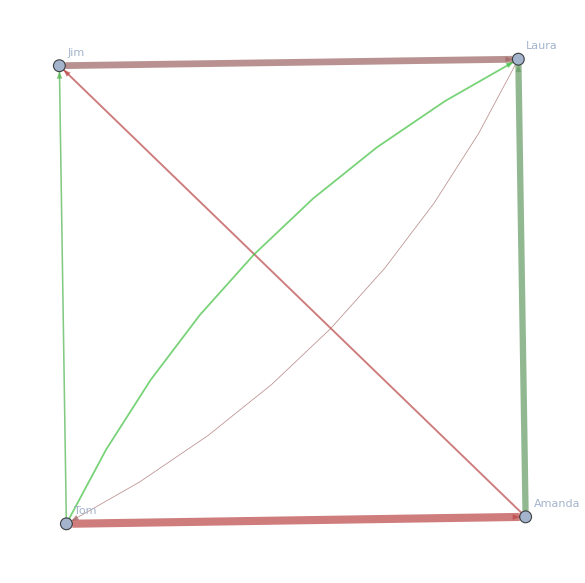

-Graphics-

{Amanda,Tom,Laura,Jim}

```mathematica
edgeThickness=Thread[viableRules->(Thickness[#]&/@viableThickness)];
edgeFormat=Table[viableRules⟦i⟧->Directive[Values[edgeThickness]⟦i⟧,Values[edgeColors]⟦i⟧],{i,1,Length[edgeColors]}];
g=Graph[nameList,viableRules,VertexLabels->All,EdgeStyle->edgeFormat]
cgp=CommunityGraphPlot[g]
nameList
```

```mathematica
lines
```

{  Tom? Yes, Mother.
, We can't say grace until you come to the table!
, Coming, Mother. 
,  Honey, don't push with your fingers. If you have to push with
something, the thing to push with is a crust of bread. And chew !chew! Animals have sections in
their stomachs which enable them to digest flood without mastication, but human beings are 
supposed to chew their food before they swallow it down. Eat food leisurely, son, and really
enjoy it. A well-cooked meal has lots of delicate flavours that have to be held in the mouth for
appreciation. So chew your food and give your salivary glands a chance to function !

, I haven't enjoyed one bite of this dinner because of your constant directions on how to eat
it. It's you that makes me rush through meals with your hawk-like attention to every bite I take.
Sickening - spoils my appetite - all this discussion of - animals' secretion - salivary glands -
mastication !
,  Temperament like a Metropolitan star ! 
You're not excused from the table.
, I'm getting a cigarette.
, You smoke too much.

, I'll bring in the blancmangé.

,  No, sister, no, sister - you be the lady this time and I'll be the darkey
, I'm already up.
, Resume your seat, little sister, I want you to stay fresh and pretty for gentleman
callers!
, I'm not expecting any gentleman callers.
,  Sometimes they come when they are least
expected! Why, I remember one Sunday afternoon in Blue Mountain -
, I know what's coming
, Yes. But let her tell it.
, Again?
, She loves to tell it.

, One Sunday afternoon in Blue Mountain, your mother received seventeen!
gentlemen callers! Why, sometimes there weren't chairs enough to accommodate them all. We
had to send the nigger over to bring in folding chairs from the parish house.
,  How did you entertain those gentleman callers?
,: I understood the art of conversation !
, I bet you could talk.
, Girls in those days knew how to talk, I can tell you.
, Yes?

, They knew how to entertain their gentlemen callers. It wasn't enough for a girl to be
possessed of a pretty face and a graceful figure although I wasn't alighted in either respect. She
also needed to have a nimble wit and a tongue to meet all occasions.
, What did you talk about?
, Things of importance going on in the world ! Never anything coarse or common or
vulgar.
 
My callers were gentleman -all! Among my callers were some of the most prominent young
planters of the Mississippi Delta - planters and sons of planters!

There was young Champ Laughlin who later became vice-president of the Delta Planters Bank.
Hadley Stevenson who was drowned in Moon Lake and left his widow one hundred and fifty
thousand in Government bonds.
There were the Cutrere brothers, Wesley and Bates. Bates was one of my bright particular beaux!
He got in a quarrel with that wild Wainwright boy. They shot it out on the floor of Moon Lake
Casino. Bates was shot through the stomach. Died in the ambulance on his way to Memphis. His
widow was also well provided for, came into eight or ten thousand acres, that's all. She married
him on the rebound - never loved her - carried my picture on him the night he died !And there
was that boy that every girl in the Delta had set her cap for! That brilliant, brilliant young
Fitzhugh boy from Greene County!
, What did he leave his widow?
, He never married ! Gracious, you talk as though all of my old admirers had turned
up their toes to the daisies !
, Isn't this the first you've mentioned that still survives ?
, That Fitzhugh boy went North and made a fortune - came to be known as the Wolf
of Wall Street! He had the Midas touch, whatever he touched turned to gold!
And I could have been Mrs Duncan J. Fitzhugh, mind you! But - I picked your father !
,  Mother, let me clear the table.
, No, dear, you go in front and study your typewriter chart. Or practise your shorthand
a little. Stay fresh and pretty! It's almost time for our gentlemen callers to start arriving.  How many do you suppose we're going to entertain
this afternoon?

,  I don't believe we're going to receive any, Mother.
,  What? Not one - not one? You must be joking!


Not one gentleman caller? It can't be true ! There must be a flood, there must have been a
tornado!
, It isn't a flood, it's not a tornado, Mother. I'm just not popular like you were in Blue
Mountain. ...  Mother's afraid I'm going to be an old maid.

, is seated in the delicate ivory chair at the small claw-foot table.
She wears a dress of soft violet material for a kimono - her hair tied back from her forehead with
a ribbon.
She is washing and polishing her collection of glass.
, appears on the fire-escape steps. At the sound of her ascent, Laura catches her
breath, thrusts the bowl of ornaments away and seats herself stiffly before the diagram of the
typewriter keyboard as though it held her spellbound.
Something has happened to Amanda. It is written in her face as she climbs to the landing: a
look that is grim and hopeless and a little absurd.
She has on one of those cheap or imitation velvety-looking cloth coats with imitation fur collar.
Her hat is five or six years old, one of those dreadful cloche hats that were worn in the late
twenties and she is eloping an enormous black patent-leather pocketbook with nickel clasps and
initials. This is her full-dress outfit, the one she usually wears to the D.A.R.
Before entering she looks through the door.
She purses her lips, opens her eyes very wide, rolls them upward, and shakes her head.
Then she slowly lets herself in the door. Seeing her mother's expression , touches her lips
with a nervous gesture.]
, Hello, Mother, I was - 
,: Deception ? Deception ? 
,  How was the DAR. meeting?  Didn't you go to the DAR. meeting, Mother?
,  - No. - No.  I did not have the
strength - to go to the DAR. In fact, I did not have the courage! I wanted to find a hole in the
ground and hide myself in it for ever ! 
,  Why did you do that, Mother?  Why are you ??
, Why? Why? How old are you, Laura?
, Mother, you know my age.
, I thought that you were an adult; it seems that I was mistaken. 
, Please don't stare at me, Mother.

, What are we going to do, what is going to be. come of us, what is the future?

, Has something happened, Mother?  Mother, has - something happened?
, I'll be all right in a minute, I'm just bewildered  - by life. ...
, Mother, I wish that you would tell me what's happened!
,: As you know, I was supposed to be inducted into my office at the D.A.R. this
afternoon.  But I stopped off at Rubicam's business
college to speak to your teachers about your having a cold and ask them what progress they
thought you were making down there.
, Oh....
, I went to the typing instructor and introduced myself as your mother. She didn't
know who you were. Wingfield, she said. We don't have any such student enrolled at the school!
I assured her she did, that you had been going to classes since early in January.
'I wonder,' she said, 'if you could be talking about that terribly shy little girl who dropped out of
school after only a few days' attendance?'
'No,' I said, 'Laura, my daughter, has been going to school every day for the past six weeks !'
'Excuse me,' she said. She took the attendance book out and there was your name, unmistakably
printed, and all the dates you were absent until they decided that you had dropped out of school.
I still said, 'No, there must have been some mistake I There must have been some mix-up in the
records !'
And she said, 'No - I remember her perfectly now. Her hands shook so that she couldn't hit the
right keys ! The first time we gave a speed-test, she broke down completely - was sick at the
stomach and almost had to be carried into the wash-room! After that morning she never showed
up any more. We phoned the house but never got any answer' -while I was working at Famous
and Barr, I suppose, demonstrating those - Oh!
I felt so weak I could barely keep on my feet !
I had to sit down while they got me a glass of water !
Fifty dollars' tuition, all of our plans - my hopes and ambition for you - just gone up the spout,
just gone up the spout like that. 
What are you doing?
, Oh I 
, Laura, where have you been going when you've gone on pretending that you were
going to business college ?
L A U RA: I've just been going out walking.
, That's not true.
, It is. I just went walking.
, Walking? Walking? In winter? Deliberately courting pneumonia in that light coat?
Where did you walk to, Laura?
, All sorts of places - mostly in the park.
, Even after you'd started catching that cold?
, It was the lesser of two evils, Mother.  I
couldn't go back up. I threw up -on the floor !
, From half past seven till after five every day you mean to tell me you walked around
in the park, because you wanted to make me think that you were still going to Rubicam's
Business College?
, It wasn't as bad as it sounds. I went inside places to get warmed up.
, Inside where?
, I went in the art museum and the bird-houses at the Zoo. I visited the penguins every
day! Sometimes I did without lunch and went to the movies. Lately I've been spending most of
my afternoons in the jewel-box, that big glass-house where they raise the tropical flowers.
, You did all this to deceive me, just for deception?  Why?
, Mother, when you're disappointed, you get that awful suffering look on your face, like
the picture of Jesus' mother in the museum !
, Hush !
, I couldn't face it.

,  So what are we going to do the rest of
our lives? Stay home and watch the parades go by? Amuse ourselves with the glass menagerie,
darling? Eternally play those worn-out phonograph records your father left as a painful reminder
of him? We won't have a business career - we've given that up because it gave us nervous
indigestion !  What is there left but dependency all our lives? I know so well
what becomes of unmarried women who aren't prepared to occupy a position. I've seen such
pitiful cases in the South - barely tolerated spinsters living upon the grudging patronage of
sister's husband or brother's wife ! - stuck away in some little mousetrap of a room - encouraged
by one in-law to visit another - little birdlike women without any nest - eating the crust of
humility all their life !
Is that the future that we've mapped out for ourselves? I swear it's the only alternative I can think
of !
It isn't a very pleasant alternative, is it? Of course - some girls do marry!

Haven't you ever liked some boy?
, Yes. I liked one once.  I came across his picture a while ago.
, . He gave you his picture?
, No, it's in the year-book.
,  Oh - a high-school boy.

, Yes. His name was Jim. 
Here he is in The Pirates of Penzance.
,  The what?
, The operetta the senior class put on. He had a wonderful voice and we sat across the
aisle from each other Mondays, Wednesdays, and Fridays in the Aud. Here he is with the silver
cup for debating !See his grin?
,  He must have had a jolly disposition.
, He used to call me - Blue Roses.

, Why did he call you such a name as that?
, When I had that attack of pleurosis - he asked me what was the matter when I came
back. I Said pleurosis he thought that I said Blue Roses ! So that's what he always called me after
that. Whenever he saw me, he'd holler, 'Hello, Blue Roses ! I didn't care for the girl that he went
out with. Emily Meisenbach. Emily was the best-dressed girl at Soldan. She never struck me,
though, as being sincere. . . . It says in the Personal Section - they're engaged. That's - six years
ago ! They must be married by now.
, Girls that aren't cut out for business careers usually wind up married to some nice
man.  Sister, that's what you'll do !

, But, Mother
, Yes ? 
,  I'm - crippled !

, Nonsense ! Laura, I've told you never, never to use that word. Why, you're not
crippled, you just have a little defect - hardly noticeable, even! When people have some slight
disadvantage like that, they cultivate other things to make up for it - develop charm - and
vivacity and - charm! That's all you have to do ! One thing
your father had plenty of - was charm!



, After the fiasco at Rubicam's Business College, the idea of getting a gentleman caller for
Laura began to play a more and more important part in Mother's calculations. It became an
obsession. Like some archetype of the universal unconscious, the image of the gentleman caller
haunted our small apartment. ...
IMAGE: YOUNG MAN AT DOOR WITH FLOWERS.]
An evening at home rarely passed without some allusion to this image, this spectre, this hope.
Even when he wasn't mentioned, his presence hung in Mother's preoccupied look and in my
sister's frightened, apologetic manner - hung like a sentence passed upon the Wingfields !
Mother was a woman of action as well as words.
She began to take logical steps in the planned direction. Late that winter and in the early spring -
realizing that extra money would be needed to properly feather the nest and plume the bird - she
conducted a vigorous campaign on the- telephone, roping in subscribers to one of those
magazines for matrons called The Home-maker's Companion, the type of journal that features
the serialized , sublimations of ladies of letters who think in terms of delicate cup-like breasts,
slim, tapering waists, rich, creamy thighs, eyes like wood-smoke in autumn, fingers that soothe
and caress like strains of music, bodies as powerful as Etruscan sculpture.


,: Ida Scott? This is Amanda Wingfield! We missed you at the D.A.R. last
Monday! I said to myself: She's probably suffering with that sinus condition ! How is that sinus
condition? Horrors ! Heaven have mercy !- You're a Christian martyr, yes, that's what you are, a
Christian martyr !
Well, I just have happened to notice that your subscription to the Companion's about to expire!
Yes, it expires with the next issue, honey !- just when that wonderful new serial by Bessie Mae
Hopper is getting off to such an exciting start. Oh, honey, it's something that you can't miss !You
remember how 'Gone With the Wind' took everybody by storm? You simply couldn't go out if
you hadn't read it. All everybody talked was Scarlet O'Hara. Well, this is a book that critics
already compare to Gone With the Wind. It's the 'Gone With the Wind' of the post-World War
generation! - What? -Burning !- Oh, honey, don't let them bum, go take a look in the oven and
I'll hold the wire! Heavens - I think she's hung up !



, What in Christ's name am !
,  Don't you use that -
, Supposed to do !
, Expression !Not in my -
, Ohhh! !
, Presence ! Have you gone out of your senses?
, I have, that's true, driven out !
, What is the matter with you, you - big - big IDIOT !
, Look !- I've got no thing, no single thing !
, Lower Your Voice !
, In my life here that I can call my OWN ! Everything is -
, Stop that shouting !
, Yesterday you confiscated my books ! You had the nerve to -
, I took that horrible novel back to the library- yes ! That hideous book by that insane
Mr. Lawrence.  I cannot control the output of diseased minds or people who
cater to them -  BUT I WON'T ALLOW SUCH FILTH
BROUGHT INTO MY HOUSE ! NO, no, no, no, no !
, House, house ! Who pays rent on it, who makes a slave of himself to -
,  Don't you DARE to -
, No, no, I mustn't say things ! I've got to just -
, Let me tell you Tom I don't want to hear any more! 

, You will hear more, you -
, No, I won' t hear more, I'm going out !
, You come right back in -
, Out, out, out ! Because I'm -
,: Come back here, Tom Wingfield ! I'm not through talking to you !
, Oh, go -
,  Tom !
, You're going to listen, and no more insolence from you ! I'm at the end of my
patience !

, What do you think I'm at? Aren't I supposed to have any patience to reach the end of,
Mother? I know, I know. It seems unimportant to you, what I'm doing - what I want to do -
having a little difference between them !You don't think that -
, I think you've been doing things that you're ashamed of. That's why you act like this.
I don't believe that you go every night to the movies. Nobody goes to the movies night after
night. Nobody in their right mind goes to the movies as often as you pretend to. People don't go
to the movies at nearly midnight, and movies don't let out at two a.m. Come in stumbling.
Muttering to yourself like a maniac! You get three hours' sleep and then go to work. Oh, I can
picture the way you're doing down there. Moping, doping, because you're in no condition.
,  No, I'm in no condition !
, What right have you got to jeopardize your job - jeopardize the security of us all?
How do you think we'd manage if you were -
, Listen !You think I'm crazy about the warehouse?  You think I'm in love with the Continental Shoemakers? You think I want to spend fifty-
five years down there in that - celotex interior! with - fluorescent - tubes! Look! I'd rather
somebody picked up a crowbar and battered out my brains - than go back mornings! I go ! Every
time you come in yelling.85.85.85
that God damn 'Rise and Shine!'- 'Rise and Shine!' I say to myself, 'How lucky dead people are !
'But I get up. I go! For sixty-five dollars a month I give up all that I dream of doing and being
ever! And you say self - selfs' all I ever think of. Why, listen, if self is what I thought of, Mother,
I'd be where he is -G 0 N E !  As far as the system of transportation
reaches !  Don't grab at me, Mother !
, Where are you going?
, I'm going to the movies!
, I don't believe that lie !
,  I'm going
to opium dens ! Yes, opium dens, dens of vice and criminals' hang-outs, Mother. I've joined the
Hogan gang, I'm a hired assassin, I carry a tommy-gun in a violin case! I run a string of cathouses in the Valley! They call me Killer, Killer Wingfield, I'm leading a double-life, a simple,
honest warehouse worker by day, by night a dynamic tsar of the underworld, Mother. I go to
gambling casinos, I spin away fortunes on the roulette table ! I wear a patch over one eye and a
false moustache, sometimes I put on green whiskers. On those occasions they call me -El Diablo
! Oh, I could tell you things to make you sleepless ! My enemies plan to dynamite this place.
They're going to blow us all sky-high some night ! I'll be glad, very happy, and so will you !
You'll go up, up on a broomstick, over Blue Mountain with seventeen gentlemen callers! You
ugly - babbling old - witch. 

,  : My glass ! - menagerie. . . . 

,  I won't speak to you - until you apologize ! 


, : One crack -and it falls through !

, Tom ! Tom, what are you doing?
, Looking for a door-key.
, Where have you been all this time?
, I have been to the movies.
, All this time at the movies?
TO M: There was a very long programme. There was a Garbo picture and a Mickey Mouse and a
travelogue and a newsreel and a preview of coming attractions. And there was an organ solo and
a collection for the milk-fund - simultaneously - which ended up in a terrible fight between a fat
lady and an usher !
,  Did you have to stay through everything?
, Of course ! And, oh, I forgot ! There was a big stage show ! The headliner on this stage
show was Malvolio the
Magician. He performed wonderful tricks, many of them, such as pouriing water back and forth
between pitchers.
First it turned to wine and then it turned to beer and then it turned to whisky. I knew it was
whisky it finally turned
into because he needed somebody to come up out of the audience to help him, and I came up -
both shows ! It was
Kentucky Straight Bourbon. A very generous fellow, he gave souvenirs. (He pulls from his back
pocket a shimmering
rainbow-coloured scarf.) He gave me this. This is his magic scarf. You can have it, Laura. You
wave it over a canary
cage and you get a bowl of gold- fish. You wave it over the gold-fish bowl and they fly away
canaries. . . . But the
wonderfullest trick of all was the coffin trick. We nailed him into a coffin and he got out of the
coffin without rernoving one nail,  There is a trick that would come in
handy for me - get me out of this 2 by 4 situation ! 
, Tom ? Shhh'!
TO M: What're you shushing me for?
, You'll wake up mother.
, Goody, goody ! Pay 'er back for all those 'Rise an' Shines'.  You
know it don't take much intelligence to get yourself into a nailed-up coffin, Laura. But who in
hell ever got himself out of one without removing one nail?



,  I'll rise -but I won't shine

, Laura, tell your brother his coffee is ready.

, Tom!- It's nearly seven. Don't make mother nervous.  Tom, speak to mother this morning. Make up with her, apologize, speak to her !
, She won't to me. It's her that started not speaking.
, If you just say you're sorry she'll start speaking.
, Her not speaking - is that such a tragedy?
, Please - please !
,  Laura, are you going to do what I asked you to do, or do I
have to get dressed and go out myself?
, Going, going - soon as I get on my coat ! Butter and what else?
,  Just butter. Tell them to charge it.
, Mother, they make such faces when I do that
, Sticks and stones can break our bones, but the expression on Mr Garfinkel's face
won't harm us ! Tell your his coffee is getting cold.
,  Do what I asked you, will you, will you,
,?

, Laura, go now or just don't go at all !
,  Going -going! 
, Laura?
, I'm all right. I slipped, but I'm all right.
,  If anyone breaks a leg on those fire-escape steps, the
landlord ought to be sued for every cent he possesses ! 

,  Mother. ! - I apologize, Mother.  I'm sorry for what I said, for
everything that I said; I didn't mean it.
,  My devotion has made me a witch and so I make myself hateful to my
children !
, NO, you don't.
, I worry so much, don't sleep, it makes me nervous!
,  I understand that.
, I've had to put up a solitary battle all these years. But you're my right-hand bower !
Don't fall down, don't fail !
,  I try, Mother.
,  Try and you will suCCEED !  Why, you -you're just full of natural endowments ! Both of my children - they're
unusual children ! Don't you think I know it? I'm so proud! Happy and - feel I've - so much to be
thankful for but - Promise me one thing, Son !
, What, Mother?
, Promise, Son, you'll - never be a drunkard !
,  I will never be a drunkard, Mother.
, That's what frightened me so, that you'd be drinking ! Eat a bowl of Purina !
, Just Coffee, Mother.
, Shredded wheat biscuit?
Tom: No. No, Mother, just coffee.
, You can't put in a day's work on an empty stomach. You've got ten minutes - don't
gulp ! Drinking
too hot liquids makes cancer of the stomach. Put cream in.
, No, thank you.
, To cool it.
, . No! No, thank you, I want it black.
, I know, but it's not good for you. We have to do all that we can to build ourselves
up. In these trying times we live in, all that we have to cling to is - each other. . . . That's why it's
so important to - Tom, ! - I sent out your sister so I could discuss something with you. If you
hadn't spoken I would have spoken to you. 
,  What is it, Mother, that you want to discuss?
, Laura!

, - Oh. - Laura ...
,  You know how Laura is. So quiet but - still water runs deep !
She notices things and I think she - broods about them.  A few days ago I came
in and she was crying.
, What about?
, YOU.
, Me?
, She has an idea that you're not happy here
, What gave her that idea?
, What gives her any idea? However, you do act strangely. ! - I'm not criticizing,
understand that! I know your ambitions do not lie in the warehouse, that like everybody in the
whole wide world - you've had to make sacrifices, but - Tom - Tom - life's not easy, it calls for -
Spartan endurance ! There's so many things in my heart that I cannot describe to you ! I've never
told you but - I loved your father. . . .
,  : I know that, Mother.
, And you - when I see you taking after his ways ! Staying out late - and - well, you
had been drinking the night you were in that - terrifying condition ! Laura says that you hate the
apartment and that you go out nights to get away from it! Is that true, Tom?
, No. You say there's so much in your heart that you can't describe to me. That's true of me,
too. There's so much in my heart that I can't describe to"you! So let's respect each other's -
, But, why - why, Tom - am you always so restless? Where do you go to, nights?
, I - go to the movies.
, Why do you go to the movies so much, Tom?
TO M: I go to the movies because - I like adventure
Adventure is something I don't have much of at work, so I go to the movies.
, But, Tom, you go to the movies entirely too much !
, I like a lot of adventure.

, Most young men find adventure in their careers.
, Then most young men are not employed in a warehouse.
, The world is full of young men employed in warehouses and offices and factories.
, Do all of them find adventure in their careers?
, They do or they do without it! Not everybody has a craze for adventure.
, Man is by instinct a lover, a hunter, a fighter, and none of those instincts are given much
play at the warehouse !
, Man is by instinct! Don't quote instinct to me! Instinct is something that people have
got away from ! It belongs to animals ! Christian adults don't want it !
, , What do Christian adults want, then, Mother?
, Superior things! Things of the mind and the spirit ! Only animals have to satisfy
instincts ! Surely your aims are somewhat higher than theirs ! Than monkeys - pigs
, I reckon they're not.
, You're joking. However, that isn't what I wanted to discuss.
,  I haven't much time.
,  Sit down.
, You want me to punch in red at the warehouse, Mother?
, You have five minutes. I want to talk about Laura.

, All right! What about Laura?
, We have to be making some plans and provisions for her. She's older than you, two
years, and nothing has happened. She just drifts along doing nothing. It frightens me terribly how
she just drifts along.
, I guess she's the type that people call home girls.
, There's no such type, and if there is, it's a pity ! That is unless the home is hers, with
a husband !
, What?
, Oh, I can see the handwriting on the wall as plain as I see the nose in front of my
face ! It's terrifying ! More and more you remind me of your father ! He was out all hours
without explanation ! - Then left ! Good-bye ! And me with the bag to hold. I saw that letter you
got from the Merchant Marine. I know what you're dreaming of. I'm not standing here
blindfolded.
Very well, then. Then, do it ! But not till there's somebody to take your place.
, What do you mean?
, I mean that as soon as Laura has got somebody to take care of her, married, a home
of her own, independent ?- why, then you'll be free to go wherever you please, on land, on sea,
whichever way the wind blows you !
But until that time you've got to look out for your sister. I don't say me because I'm old and don't
matter - I say for your sister because she's young and dependent.
I put her in business college - a dismal failure ! Frightened her so it made her sick at the stomach.
I took her over to the Young Peoples League at the church. Another fiasco. She spoke to nobody,
nobody spoke to her. Now all she does is fool with those pieces of glass and play those worn-out
records. What kind of a life is that for a girl to lead?
, What can I do about it?
, Overcome Selfishness ! Self, self, self is all that you ever think of !

Where is your muffler? Put your wool muffler on !  Tom ! I haven't said what I had in mind to
ask you.
, I'm too late to
,  Down at the warehouse, aren't
there some - nice young men?
, No !
, There must be - some
, Mother 
, Find out one that's clean-living - doesn't drink and - ask him out for sister !
, What?
, For sister ! To meet ! Get acquainted
,  Oh, my go- osh !
, Will you?  Will you?  Will you? Will
you, dear?
,  YES !

, Ella Cartwright? This is Amanda Wingfield !How are you, honey?
How is that kidney condition?

Horrors!

You're a Christian martyr, yes, honey, that's what you are, a Christian martyr!
Well, I just now happened to notice in my little red book that your subscription to the
Companion has just run out! I knew that you wouldn't want to miss out on the wonderful serial
starting in this issue. It's by Bessie Mae Hopper, the first thing she's written since Honeymoon
for Three.
Wasn't that a strange and interesting story? Well, this one is even lovelier, I believe. It has a
sophisticated, society background. It's all about the horsy set on Long Island!


,  Son, Will you do me a favour?
, What?
, Comb your hair! You look so pretty when your hair is combed!  There is only one respect in
which I would like you to emulate your father.
, What respect is that?
, The care he always took of his appearance. He never allowed himself to look untidy.
 Where are you going?
, I'm going out to smoke.
, You smoke too much. A pack a day at fifteen cents a pack. How much would that
amount to in a month? Thirty times fifteen is how much, Tom? Figure it out and you will be
astounded at what you could save. Enough to give you a night-school course in accounting at
Washington U ! Just think what a wonderful thing that would be for you, Son !

, I'd rather smoke. 
,  I know !That's the tragedy of it. 

,  Across the alley from us was the Paradise Dance Hall. On evenings in
spring the windows and doors were open and the music came outdoors. Sometimes the lights
were turned out except for a large glass sphere that hung from the ceiling. It would turn slowly
about and filter the dusk with delicate rainbow colours. Then the orchestra played a waltz or a
tango, something that had a slow and sensuous rhythm. Couples would come outside, to the
relative privacy of the alley. You could see them kissing behind ash-pits and telegraph poles.
This was the compensation for lives that passed like mine, without any change or adventure.
Adventure and change were imminent in this year. They were waiting around the corner for all
these kids.
Suspended in the mist over Berchtesgaden, caught in the folds of Chamberlain's umbrella. In
Spain there was Guernica!
But here there was only hot swing music and liquor, dance halls, ban, and movies, and sex that
hung in the gloom like a chandelier and flooded the world with brief, deceptive rainbows. ...
All the world was waiting for bombardments !

,  A fire-escape landing's a poor excuse for a porch.  What are you looking at?
, The moon.
, Is there a moon this evening?
, It's rising over Garfinkel's Delicatessen.
, So it is ! A little silver slipper of a moon. Have you made a wish on it yet?
, Um-hum.
, What did you wish for?
, That's a secret.
, A secret, huh? Well, I won't tell mine either. I will be just as mysterious as you.
, I bet I can guess what yours is.
, Is my head so transparent?
, You're not a sphinx.
, No, I don't have secrets. I'll tell you what I wished for on the moon. Success and
happiness for my precious children! I wish for that whenever there's a moon, and when there isn't
a moon, I wish for it, too.
, I thought perhaps you wished for a gentleman caller.
, Why do you say that?
, Don't you remember asking me to fetch one?
, I remember suggesting that it would be nice for your sister if you brought home
some nice young
from the warehouse. I think that I've made that suggestion more than once.
, Yes, you have made it repeatedly.
, Well?
, We are going to have One.
, What?
, A gentleman caller !

, You mean you have asked some nice young man to come over?
, Yep. I've asked him to dinner.
, You really did?
, I did !
, You did, and did he - accept?
, He did !
, Well, Well ? Well, well ! That's -lovely !
, I thought that you would be pleased.
, It's definite, then?
, Very definite.
, Soon?
, Very soon.
, For heaven's sake, stop putting on and tell me some things, will you?
, What things do you want me to tell you?
, Naturally I would like to know when he's coming!
, He's coming tomorrow.
, Tomorrow?
, Yep. Tomorrow.
, But, Tom !
, Yes, Mother?
, Tomorrow gives me no time I
, Time for what?
, Preparations! Why didn't you phone me at once, as soon as you asked him, the
minute that he accepted? Then, don't you see, I could have been getting ready!
, You don't have to make any fuss.
, Oh, Tom, Tom, Tom, of course I have to make a fuss! I want things nice, not
sloppy! Not thrown together. I'll certainly have to do some fast thinking, won't I?
, I don't see why you have to think at all.
, You just don't know. We can't have a gentleman caller in a pigsty ! All my wedding
silver has to be polished, the monogrammed table linen ought to be laundered ! The windows
have to be washed and fresh curtains put up. And how about clothes? We have to wear
something, don't we?
, Mother, this boy is no one to make a fuss over !
, Do you realize he's the first young man we've introduced to your sister?It's terrible,
dreadful, disgraceful that poor little sister has never received a single gentleman caller ! Tom,
come inside! 
, What for?
, I want to ask you some things.
, If you're going to make such a fuss, I'll call it off, I'll tell him not to come !
, You certainly won't do anything of the kind. Nothing offends people worse than
broken engagements. It simply means I'll have to work like a Turk ! We won't be brilliant, but
we will pass inspection. Come on inside.  Sit down.
, Any particular place you would like me to sit?
, Thank heavens I've got that new sofa ! I'm also making payments on a floor lamp I'll
have sent out ! And put the chintz covers on, they'll brighten things up ! Of course I'd hoped to
have these walls re-papered. ... What is the young man's name?
, His name is O'Connor.
, That, of course, means fish- tomorrow is Friday ! I'll have that salmon loaf - with
Durkee's dressing ! What does he do? He works at the warehouse?
, Of course ! How else would -
, Tom, he - doesn't drink?
, Why do you ask me that?
, Your father did!
, Don't get started on that !
, He does drink, then?
, Not that I know of !
, Make sure, be certain ! The last thing I want for my daughter's a boy who drinks !
, Aren't you being a little bit premature? Mr O'Connor has not yet appeared on the scene !
, But will tomorrow. To meet your sister, and what do I know about his character?
Nothing ! Old maids are better off than wives of drunkards !
, Oh, my God !
, Be still !
,  Lots of fellows meet girls whom they don't marry !
, Oh, talk sensibly, Tom - and don't be sarcastic !

, What are you doing?
, I'm brushing that cow-lick down ! What is this young man's position at the
warehouse?
,  This young man's position is that of
a shipping clerk, Mother.
, Sounds to me like a fairly responsible job, the sort of a job you would be in if you
just had more get-up.
What is his salary? Have you any idea?
, I would judge it to be approximately eighty-five dollars a month.
, Well - not princely, but
, Twenty more than I make.
, Yes, how well I know! But for a family man, eighty-five dollars a month is not
much more than you can just get by on. . . .
, Yes. but Mr O'Connor is not a family man.
, He might be, mightn't he? Some time in the future ?
, I see. Plans and provisions.
, You are the only young man that I know of who ignores the fact that the future
becomes the present, the present the past, and the past turns into everlasting regret if you don't
plan for it!
, I will think that over and see what I can make of it.
, Don't be supercilious with your mother ! Tell me some more about this - what do
you call him?
, James D. O'Connor. The D. is for Delaney.
, Irish on both sides! Gracious! And doesn't drink?
, Shall I call him up and ask him right this minute?
, The only way to find out about those things is to make discreet inquiries at the
proper moment. When I was a girl in Blue Mountain and it was suspected that a young man
drank, the girl whose attentions he had been receiving, if any girl was, would sometimes speak to
the minister of his church, or rather her father would if her father was living, and sort of feel him
out on the young man's character. That is the way such things are discreetly handled to keep a
young woman from making a tragic mistake !
, Then how did you happen to make a tragic mistake !
, That innocent look of your father's had everyone fooled ! He smiled - the world was
enchanted !
No girl can do worse than put herself at the mercy of a handsome appearance !
I hope that Mr O'Connor is not too good-looking.
, No, he's not too good-looking. He's covered with freckles and hasn't too much of a now.
, He's not right-down homely, though?
, Not right-down homely. Just medium homely, I'd say.
, Character's what to look for in a man.
, That's what I've always said, Mother.
, You've never said anything of the kind and I suspect you would never give it a
thought.
, Don't be so suspicious of me.
, At least I hope he's the type that's up and coming.
, I think he really goes in for self-improvement.
, What reason have you to think so?
, He goes to night school.
,  Splendid ! What does he do, I mean study ?
, Radio engineering and public speaking !
, Then he has visions of being advanced in the world! Any young man who studies
public speaking is aiming to have an executive job some day !
And radio engineering- A thing for the future !
Both of these facts are very illuminating. Those are the sort of things that a mother should know
concerning any young man who comes to call on her daughter. Seriously or - not.
, One little warning. He doesn't know about Laura. I didn't let on that we had dark ulterior
motives. I just said, why don't you come and have dinner with us? He said okay and that was the
whole conversation.
, I bet it was! You're eloquent as an oyster.
However, he'll know about Laura when he gets here. When he sees how lovely and sweet and
pretty she is, he'll thank his lucky stars be was asked to dinner.
, Mother, you mustn't expect too much of Laura.
, What do you mean?
, Laura seems all those things to you and me because she's ours and we love her. We don't
even notice she's crippled any more.
, Don't say crippled ! You know that I never allow that word to be used !
, But face facts, Mother. She is and - that's not all
, What do you mean "not all'?
, Laura is very different from other girls
, I think the difference is all to her advantage.
, Not quite all - in the eyes of others - strangers - she's terribly shy and lives in a world of
her own and those things make her seem a little peculiar to people outside the house.
, Don't say peculiar.
, Face the facts. She is.

, In what way is she peculiar - may I ask?
,  She lives in a world of her own - a world of little glass ornaments, Mother. . . .
 She plays old
phonograph records and - that's about all - 
,  Where are you going?
, I'm going to the movies. 
, Not to the movies, every night to the movies!  I
don't believe you always go to the movies! 
Laura ! Laura !
, Yes, Mother.
, Let those dishes go and come in front ! 
Laura, come here and make a wish on the moon !

,  Moon - moon?
, A little silver slipper of a moon. Look over your left shoulder, Laura, and make a
wish !
 Now ! Now, darling, wish !
, What shall I wish for, Mother?
,  Happiness ! Good
fortune !

CURTAIN

, And so the following evening I brought Jim home to dinner. I had known Jim slightly in
high school. In high school Jim was a hero. He had tremendous Irish good nature and vitality
with the scrubbed and polished look of white chinaware. He seemed to move in a continual
spotlight. He was a star in basket-ball, captain of the debating club, president of the senior class
and the glee club and he sang the male lead in the annual light operas. He was always running or
bounding, never just walking. He seemed always at the point of defeating the law of gravity. He
was shooting with such velocity through his adolescence that you would logically expect him to
arrive at nothing short of the White House by the time he was thirty. But Jim apparently ran into
more interference after his graduation from Soldan. His speed had definitely slowed. Six years
after he left high school he was holding a job that wasn't much better than mine.

He was the only one at the warehouse with whom I was on friendly terms. I was valuable to him
as someone who could remember his former glory, who had seen him win basketball games and
the silver cup in debating. He knew of my secret practice of retiring to a cabinet of the washroom
to work on poems when business was slack in the warehouse. He called me Shakespeare. And
while the other boys in the warehouse regarded me with suspicious hostility, Jim took a
humorous attitude toward me. Gradually his attitude affected the others, their hostility wore off
and they also began to smile at me as people smile at an oddly fashioned dog who trots across
their path at some distance.
I knew that Jim and Laura had known each other at Soldan, and I had heard Laura speak
admiringly of his voice. I didn't know if Jim remembered her or not. In high school Laura had
been as unobtrusive as Jim had been astonishing. If he did remember Laura, it was not as my
sister, for when I asked him to dinner, he grinned and said, 'You know, Shakespeare, I never
thought of you as having folks !'
He was about to discover that I did.

,  Why are you trembling?
, Mother, you've made me so nervous !
,: How have I made you nervous ?
, By all this fuss ! You make it seem so important !
, I don't understand you, Laura. You couldn't be satisfied with just sitting home, and
yet whenever I try to arrange something for you, you seem to resist it.  Now take a
look at yourself. No, wait ! Wait just a moment - I have an idea !
, What is it now?

, Mother, what are you doing?
, They call them 'Gay Deceivers'!
, I won't wear them !
, YOU Will !
, Why should I?
, Because, to be painfully honest, your chest is flat.
, You make it seem like we were setting a trap.
, All pretty girls are a trap, a pretty trap, and men expect them to be !

Now look at yourself, young lady. This is the prettiest you will ever be ! I've got. to fix myself
now ! You're going to be surprised by your mother's appearance ! 
,  I'm going to show you something. I'm going to make a spectacular
appearance I
, What is it, Mother?
, Possess your soul in patience ? you will see !
Something I've resurrected from that old trunk! Styles haven't changed so terribly much after all.

Now just look at your mother !

 This is the dress in which I led the cotillion, won the cakewalk twice at Sunset Hill,
wore one spring to the Governor's ball in Jackson !
See how I sashayed around the ballroom, Laura?

I wore it on Sundays for my gentlemen callers ! I had it on the day I met your father I had
malaria fever all that spring. The change of climate from East Tennessee to the Delta - weakened
resistance I had a little temperature all the time - not enough to be serious - just enough to make
me restless and giddy I Invitations poured in - parties all over the Delta! - 'Stay in bed,' said
mother, 'you have fever!' - but I just wouldn't. - I took quinine but kept on going, going !
Evenings, dances ! - Afternoons, long, long rides! Picnics. - lovely! - So lovely, that country in
May. - All lacy with dogwood, literally flooded with jonquils! - That was the spring I had the
craze for jonquils. Jonquils became an absolute obsession. Mother said, 'Honey, there's no more
room for jonquils.' And still I kept on bringing in more jonquils. Whenever, wherever I saw
them, I'd say, "Stop ! Stop! I see jonquils ! I made the young men help me gather the jonquils ! It
was a joke, Amanda and her jonquils ! Finally there were no more vases to hold them, every
available space was filled with jonquils. No vases to hold them? All right, I'll hold them myself -
And then I -  met your father ! Malaria fever and
jonquils and then - this - boy....
 
I hope they get here before it starts to rain.

I gave your brother a little extra change so he and Mr O'Connor could take the service car home.
,  What did you say his name was?
, O'Connor.
, What is his first name?
, I don't remember. Oh, yes, I do. It was - Jim !

,  Not - Jim!
, Yes, that was it, it was Jim ! I've never known a Jim, that wasn't nice !

, Are you sure his name is Jim O'Connor?
, Yes. Why?
, Is he the one that Tom used to know in high school?
, He didn't say so. I think he just got to know him at the warehouse.
, There was a Jim O'Connor we both knew in high school -  If that is
the one that Tom is bringing to dinner - you'll have to excuse me, I won't come to the table.
, What sort of nonsense is this?
, You asked me once if I'd ever liked a boy. Don't you remember I showed you this
boy's picture?
, You mean the boy you showed me in the year book?
, Yes, that boy.
, Laura, Laura, were you in love with that boy?
, I don't know, Mother. All I know is I couldn't sit at the table if it was him!
, It won't be him! It isn't the least bit likely. But whether it is or not, you will come to
the table. You will not be excused.
, I'll have to be, Mother.
, I don't intend to humour your silliness, Laura. I've had too much from you and your
brother, both !
So just sit down and compose yourself till they come. Tom has forgotten his key so you'll have to
let them in, when they arrive.
,  Oh, Mother - you answer the door !
,  Ill be in the kitchen - busy !
, Oh, Mother, please answer the door, don't make me do it !
,  I've got to fix the dressing for the salmon. Fuss, fuss -
silliness ! over a gentleman caller !

,  Laura, sweetheart ! The door !

, I think we just beat the rain.
, Uh - huh. 
,  Laura, that is your brother and Mr O'Connor ! Will you let them in,
darling?

,  Mother - you go to the door !

, Please, please!
,  What is the matter with you, you silly thing?
,  Please, you answer it, please !
, I told you I wasn't going to humour you, Laura. Why have you chosen this moment
to lose your mind?
, Please, please, please, you go !
,: You'll have to go to the door because I can't !
,  : I can't either !
, Why?
, I'm sick!
, I'm sick, too - of your nonsense ! Why can't you and your brother be normal people?
Fantastic whims and behaviour !

Preposterous goings on ! Can you give me one reason -  COMING! JUST
ONE SECOND! - why you should be afraid to open a door? Now you answer it, Laura !
, Oh, oh, oh ... 
, Laura Wingfield, you march right to that door !
, Yes - yes, Mother !

, Laura, this is Jim. Jim, this is my sister, Laura.
,  I didn't know that Shakespeare had a sister!
,  How - how do you do?
,  - Okay !

, Your hand's cold, Laura !
, Yes, well- I've been playing the victrola....
, Must have been playing classical music on it! You ought to play a little hot swing music to
warm you up !
, Excuse me - I haven't finished playing the victrola. ... 
,  What was the matter?
, Oh - with Laura? Laura is - terribly shy.
, Shy, huh? It's unusual to meet a shy girl nowadays. I don't believe you ever mentioned you
had a sister.
, Well, now you know. I have one. Here is the Post Dispatch. You want a piece of it?
, Uh-huh.
, What piece? The comics?
, Sports !  Ole Dizzy Dean is on his bad behaviour.
T0M  : Yeah ? 
, Where are you going?
, I'm going out on the terrace.
,  You know, Shakespeare - I'm going to sell you a bill of goods !
, What goods?
, A course I'm taking.
, Huh?
, In public speaking! You and me, we're not the warehouse type.
, Thanks - that's good news. But what has public speaking got to do with it?
, It fits you for - executive positions !
, Awww.
, I tell you it's done a helluva lot for me.

, In what respect?
, In every ! Ask yourself what is the difference between you an' me and men in the office
down front? Brains? No! - Ability? - No ! Then what? Just one little thing
, What is that one little thing?
, Primarily it amounts to - social poise! Being able to square up to people and hold your own
on any social level!
,  Tom?
, Yes, Mother?
, Is that you and Mr O'Connor?
, Well, you just make yourselves comfortable in there.
, Yes, Mother.
, Ask Mr O'Connor if he would like to wash his hands.
, Aw, no - no - thank you - I took care of that at the warehouse. Tom, Yes?
JI M: Mr Mendoza was speaking to me about you.
, Favourably?
, What do you think?
, Well
, You're going to be out of a job if you don't wake up.
, I am waking up
, You show no signs.
, The signs are interior.

, I' m planning to change.  I'm right at the point of committing myself to a future that
doesn't include the warehouse and Mr Mendoza or even a night-school course in public speaking.
, What are you gassing about?
, I'm tired of the movies.
J IM: Movies!
, Yes, movies ! Look at them ?  All of those
glamorous people - having ,adventures - hogging it all, gobbling the whole thing up ! You know
what happens? People go to the movies instead of moving! Hollywood characters are supposed
to have all the adventures for everybody in America, while everybody in America sits in a dark
room and watches them have them ! Yes, until there's a war. That's when adventure becomes
available to the masses ! Everyone's dish, not only Gable's ! Then the people in the dark room
come out of the dark room to have some adventure themselves Goody, goody! - It's our turn
now, to go to the South Sea Islands - to make a safari - to be exotic, far-off ! - But I'm not
patient. I don't want to wait till then. I'm tired of the movies and I am about to move !
,  Move?
, Yes.
, When?
, Soon !
, Where? Where?

, I'm starting to boil inside. I know I seem dreamy, but inside - well, I'm boiling ! -
Whenever I pick up a shoe, I shudder a little thinking how short life is and what I am doing! -
Whatever that means, I know it doesn't mean shoes - except as something to wear on a traveller's
feet !  Look
, What?
, I'm a member.
,  The Union of Merchant Seamen.
, I paid my dues this month, instead of the light bill.
, You will regret it when they turn the lights off.
, I won't be here.
, How about your mother?
, I'm like my father. The bastard son of a bastard! See how he grins? And he's been absent
going on sixteen years !
, You're just talking, you drip. How does your mother feel about it?
, Shhh! -
Here comes mother ! Mother is not acquainted with my plans!
,  Where are you all?
, On the terrace, Mother.

,  Well, well, well, so this is Mr O'Connor.
Introductions entirely unnecessary. I've heard so much about you from my boy. I finally said to 
him, Tom - good gracious! - why don't you bring this paragon to supper? Id like to meet this nice
young man at the warehouse! - Instead of just hearing you sing his praises so much!
I don't know why my son is so stand-offish - that's not Southern behaviour !
Let's sit down and - I think we could stand a little more air in here ! Tom, leave the door open. I
felt a nice fresh breeze a moment ago. Where has it gone to?
Mmm, so warm already ! And not quite summer, even. We're going to bum up when summer
really gets started. However, we're having - we're having a very light supper. I think light things
are better fo' this time of year. The same as light clothes are. Light clothes an' light food are what
warm weather calls fo'. You know our blood gets so thick during th' winter - it takes a while fo'
us to adjust ou'selves! - when the season changes ...
It's come so quick this year. I wasn't prepared. All of a sudden - heavens ! Already summer! - I
ran to the trunk an' pulled out this light dress - Terribly old! Historical almost! But feels so good
- so good an' co-ol, y' know....
, Mother
, Yes, honey?
, How about - supper?
,: Honey, you go ask Sister if supper is ready ! You know that Sister is in full
charge of supper! Tell her you hungry boys are waiting for it.

Have you met Laura?
, She-
, Let you in? Oh, good, you've met already! It's rare for a girl as sweet an' pretty as
Laura to be domestic! But Laura is, thank heavens, not only pretty but also very domestic. I'm
not at all. I never was a bit. I never could make a thing but angel-food cake. Well, in the South
we had so many servants. Gone, gone, gone. All vestige of gracious living ! Gone completely! I
wasn't prepared for what the future brought me. All of my gentlemen callers were sons of
planters and so of course I assumed that I would be married to one and raise my family on a large
piece of land with plenty of servants. But man proposes and woman accepts the proposal ! - To
vary that old, old saying a little bit - I married no planter! I married a man who worked for the
telephone company! - That gallantly smiling gentleman over there!  A
telephone man who - fell in love with long distance I - Now he travels and I don't even know
where ! - But what am I going on for about my - tribulations?
Tell me yours ? I hope you don't have any ! Tom?
,  Yes, Mother?
, Is supper nearly ready?
, It looks to me like supper is on the table.
, Let me look -  Oh, lovely ! - But
where is Sister?
, Laura is not feeling well - and she says that she thinks she'd better not come to the table.
, What? - Nonsense ! - Laura? Oh, Laura !
,  Yes, Mother.
, You really must come to the table. We won't be seated until you come to the table !
Come in, Mr O'Connor. You sit over there, and I'll Laura - Laura Wingfield !
You're keeping us waiting, honey ! We can't say grace. until you come to the table !

, Laura!
, Laura !.
LEGEND: ' AH!']
 Why, Laura, you are sick, darling ! Tom, help your sister into the living-room,
dear !
Sit in the living-room, Laura - rest on the sofa. Well !

Standing over the hot stove made her ill ! - I told her that was just - too warm this evening, but -

Is Laura all right now?
, Yes.
, What is that? Rain? A nice cool rain has come up!

I think we may - have grace - now ...

Tom, honey - you say grace !
, Oh ...
'For these and all thy mercies-'


, Hey, there, Mr Light Bulb !

, Where was Moses when the lights went out? Ha-ha. Do you know the answer to that
one, Mr O'Connor?
, No, Ma'am, what's the answer?
, In the dark!

Everybody sit still. I'll light the candles. Isn't it lucky we have them on the table? Where's a
match? Which of you gentlemen can provide a match?
, Here.
, Thank you, Sir.
, Not at all, Ma'am!
, I guess the fuse has burnt out. Mr O'Connor, can you tell a burnt-out fuse? I know I
can't and Tom is a total loss when it comes to mechanics.

Oh, be careful you don't bump into something. We don't want our gentleman caller to break his
neck. Now wouldn't that be a fine howdy-do?
, Ha-ha! Where is the fuse-box?
, Right here next to the stove. Can you see anything?
, just a minute.
, Isn't electricity a mysterious thing? Wasn't it Benjamin Franklin who tied a key to a
kite?
We live in such a mysterious universe, don't we? Some people say that science clears up all the
mysteries for us. In my opinion it only creates more !
Have you found it yet?
, No, Ma'am. All these fuses look okay to me.
,Tom!
, Yes, Mother?
, That light bill I gave you several days ago. The one I told you we got the notices
about?

, Oh. - Yeah.
, You didn't neglect to pay it by any chance?
, Why, I -
, Didn't ! I might have known it !
, Shakespeare probably wrote a poem on that light bill, Mrs Wingfield.
, I might have known better than to trust him with it! There's such a high price for
negligence in this world!
, Maybe the poem will win a ten-dollar prize.
, We'll just have to spend the remainder of the evening in the nineteenth century,
before Mr Edison made the Mazda lamp!
, Candlelight is my favourite kind of light.
, That shows you're romantic! But that's no excuse for Tom.
Well, we got through dinner. Very considerate of them to let us get through dinner before they
plunged us into ever-lasting darkness, wasn't it, Mr O'Connor?
, Ha-ha !
,: Tom, as a penalty for your carelessness you can help me with the dishes.
, Let me give you a hand.
,: Indeed you will not !
, I ought to be good for something.
, Good for something?  You? Why, Mr O'Connor, nobody,
nobody's given me this much entertainment in years - as you have !
, Aw, now, Mrs Wingfield !
, I'm not exaggerating, not one bit! But Sister is all by her lonesome. You go keep her
company in the parlour ! I'll give you this lovely old candelabrum that used to be on the altar at
the church of the Heavenly Rest. It was melted a little out of shape when the church burnt down.
Lightning struck it one spring.
Gypsy Jones was holding a revival at the time and he intimated that the church was destroyed
because the Episcopalians gave card parties.
, Ha-ha.
, And how about you coaxing Sister to drink a little wine? I think it would be good for
her ! Can you carry both at once?
, Sure. I'm Superman! 
, Now, Thomas, get into this apron !

, Hello, there, Laura.
,  Hello. 
, How are you feeling now? Better?
, Yes. Yes, thank you.
, This is for you. A little dandelion wine. 
, Thank you.
, Drink it - but don't get drunk!

Where shall I set the candles?
, Oh - oh, anywhere. . . ,
, -. How about here on the floor? Any objections?
,-No.
, I'll spread a newspaper under to catch the drippings. I like to sit on the floor. Mind if I do?
, Oh, no.
, Give me a pillow?
, What?
, A pillow !
,Oh ... 
, How about you? Don't you like to sit on the floor?
, Oh - yes.
, Why don't you, then?
, I - Will.
, Take a pillow !  I can't hardly see you sitting way over there.
, I can - see you.
, I know, but that's not fair, I'm in the limelight.  Good !
Now I can see you ! Comfortable?
, Yes.
, So am I . Comfortable as a cow ! Will you have some gum?
, No, thank you.
, I think that I will indulge, with your permission, 
Think of the fortune made by the guy that invented the first piece of chewing gum. Amazing, 
huh? The Wrigley Building is one of the sights of Chicago. - I saw it summer before last when I
went up to the Century of Progress. Did you take in the Century of Progress?
, No, I didn't.
, Well, it was quite a wonderful exposition. What impressed me most was the Hall of
Science. Gives you an idea of what the future will be in America, even more wonderful than the
present time is!  Your brother tells me you're shy. Is that right, Laura?
, I - don't know.
, I judge you to be an old-fashioned type of girl. Well, I think that's a pretty good type to be.
Hope you don't think I'm being too personal - do you?
,  I believe I will take a piece of gum, if you - don't mind.
 Mr O'Connor, have you - kept up with your singing?
, Singing? Me?
, Yes. I remember what a beautiful voice you had.
, When did you hear me sing?

Voice  : 0 blow, ye winds, heigh-ho,
A-roving I will go!
I'm off to my love
With a boxing glove
Ten thousand miles away !
, You say you've heard me sing?
, Oh, yes! Yes, very often I don't suppose - you remember me - at all?
,  You know I have an idea I've seen you before. I had that idea soon as
you opened the door. It seemed almost like I was about to remember your name. But the name
that I started to call you - wasn't a' name! And so I stopped myself before I said it.
, Wasn't it - Blue Roses?
,  Blue Roses ! - My gosh, yes - Blue Roses! That's what I had on my
tongue when you opened the door !
Isn't it funny what tricks your memory plays? I didn't connect you with high school somehow or
other.
But that's where it was; it was high school. I didn't even know you were Shakespeare's sister !
Gosh, I'm sorry.
, I didn't expect you to. You - barely knew me !
, But we did have a speaking acquaintance, huh?
, Yes, we - spoke to each other.
, When did you recognize me?
, Oh, right away !
, Soon as I came in the door?
, When I heard your name I thought it was probably you. I knew that Tom used to know
you a little in high school. So when you came in the door Well, then I was - sure.
, Why didn't you say something, then?
,  I didn't know what to say, I was - too surprised !
, For goodness' sakes I You know, this sure is funny !
, Yes I Yes, isn't it, though ...
, Didn't we have a class in something together?
, Yes, we did.
, What class was that?
, It was - singing - Chorus !
, Aw !
, I sat across the aisle from you in the Aud.
, Aw!
, Mondays, Wednesday, and Fridays.
, Now I remember - you always came in late.
, Yes, it was so hard for me, getting upstairs. I had that brace on my leg - it clumped so
loud I
, I never heard any clumping.
,  To me it sounded like thunder !
, Well, well, well, I never even noticed.
, And everybody was seated before I came in. I had to walk in front of all those people.
My seat was in the back row. I had to go clumping all the way up the aisle with everyone
watching I
, You shouldn't have been self-conscious.
, I know, but I was. It was always such a relief when the singing started.
, Aw, yes, I've placed you now I I used to call you Blue Rom. How was it that I got started
calling you that?
, I was out of school a little while with pleurosis. When I came back you asked me what
was the matter. I said I had pleurosis - you thought I said Blue Roses That's what you always
called me after that I
, I hope you didn't mind.
, Oh, no - I liked it. You see, I wasn't acquainted with many - people....
, As I remember you sort of stuck by yourself.
, I - I - never have had much luck at - making
friends.
, I don't see why you wouldn't.
,' . Well, I - started out badly.
, You mean being -
, Yes, it sort of - stood between me -
, You shouldn't have let it !
, I know, but it did, and -
, You were shy with people !
, I tried not to be but never could -
, Overcome it?
, No, I - I never could !
, I guess being shy is something you have to work out of
kind of gradually.
,  Yes - I guess it -
, Takes time !
, Yes -
, - People arc not so dreadful when you know them. That's what you have to remember ! And
everybody has
problems, not just you, but practically everybody has got some problems. You think of yourself
as having the only
problems, as being the only one who is disappointed. But just look around you and you will see
lots of people as
disappointed as you are. For instance, I hoped when I was going to high-school that I would be
further along at this
time, six years later, than I am now - You remember that wonderful write-up I had in The Torch?
,: Yes ! 
, It said I was bound to succeed in anything I went into!
 Holy Jeez ! The Torch ! 
,: Here you are in The Pirates of Penzance!
,  : I sang the baritone lead in that operetta.
,  So - beautifully!
,  Aw -
LAU R A: Yes, yes - beautifully - beautifully !
, You heard me?
, All three times !
, No !
, Yes !
, All three performances?
,  Yes.
, Why?
, I - wanted to ask you to - autograph my programme. 
, Why didn't you ask me to?
, You were always surrounded by your own friends so much that I never had a chance
to.
, You should have just
, Well, I - thought you might think I was
, Thought I might think you was - what?
, Oh
,  I was beleaguered by females In those days.
, You were terribly popular !
, Yeah
, You had such a - friendly way
, I was spoiled in high school. 
, Everybody - liked you !
, Including you?
, I - yes, I - I did, too - 
, Well, weH, well ! - Give me that programme, Laura.  There youare - better late than never !
, Oh, I - what a - surprise!
, My signature isn't worth very much tight now. But some day - maybe - it will increase in
value ! Being disappointed is one thing and being discouraged is something else. I am
disappointed but I am not discouraged. I'm twenty-three years old. How old are you?
,: I'll be twenty-four in June.
, That's not old age!
, No, but
, You finished high school?
,  I didn't go back. 
, You mean you dropped out?
, I made bad grades in my final examinations.  How is - Emily Meisenbach getting along?
, Oh, that kraut-head!
,: Why do you call her that ?
,: That's what she was.
, You're not still - going with her?
,: I never see her.
, It said in the Personal Section that you were engaged!
,: I know, but I wasn't impressed by that -propaganda I
, It wasn't - the truth?
,: Only in Emily's optimistic opinion ! 
, Oh

, lights a cigarette and loans indolently back on his elbows smiling at , with a warmth
and charm which lights her inwardly with altar candler. She remains by the table and turns in her
hands a piece of glass to cover her tumult.]
,  : What have you done since high school?  Huh?  I said what have you done since high school,
Laura?
,: Nothing much.
, You must have been doing something these six long years.
,Yes.
, Well, then, such as what?
, I took a business course at business college
, How did that work out?
, Well, not very - well - I had to drop out, it gave me - indigestion 
,  What are you doing now?
, I don't do anything - much. Oh, please don't think I sit around doing nothing! My glass
collection takes up agood deal of time. Glass is something you have to take good care of
, What did you say - about glass?
, Collection I said - I have one - 
,  You know what I judge to be the trouble with you?
Inferiority complex I Know what that is? That's what they call it when someone low-rates
himself !
I understand it because I had it, too. Although my caw was not so aggravated as yours seems to
be. I had it until I took up public speaking, developed my voice, and learned that I had an
aptitude for science. Before that time I never thought of myself as being outstanding in any way
whatsoever I
Now I've never made a regular study of it, but I have a friend who says I can analyse people
better than doctors that make a profession of it. I don't claim that to be necessarily true, but I can
sure guess a person's psychology, Laura I  Excuse me, Laura. I always take it
out when the flavour is gone. I'll use this scrap of paper to wrap it in. I know how it is to get it
stuck on a shoe.
Yep - that's what I judge to be your principal trouble. A lack of amount of faith in yourself as a
person. You don't have the proper amount of faith in yourself. I'm basing that fact on a number
of your remarks and also on certain observations I've made. For instance that clumping you
thought was so awful in high school. You say that you even dreaded to walk into class. You see
what you did? You dropped out of school, you gave up an education because of a clump, which
as far as I know was practically non-existent! A little physical defect is what you have. Hardly
noticeable even! Magnified thousands of times by imagination !
You know what my strong advice to you is? Think of yourself as superior in some way!
, In what way would I think?
, Why, man alive, Laura! just look about you a little. What do you see? A world full of
common people! All of 'em born and all of 'em going to die !
Which of them has one-tenth of your good points I Or mine ! Or anyone else's, as far as that goes
- Gosh !
Everybody excels in some one thing. Some in many !

All you've got to do is discover in whatl Take me, for instance.

My interest happens to lie in electro-dynamics. I'm taking a course in radio engineering at night
school, Laura, on top of a fairly responsible job at the warehouse. I'm taking that course and
studying public speaking.
, Ohhhh.
, Because I believe in the future of television !

I wish to be ready to go up right along with it. Therefore
I'm planning to get in on the ground floor. In fact I've already made the right connexions and all
that remains is for the industry itself to get under way I Full steam

Knowledge - Zzzzzp ! Money - Zzzzzzp I - Power! That's the cycle democracy is built on I

I guess you think I think a lot of myself !
, No - o-o-o, !
, Now how about you? Isn't there something you, take more interest in than anything else?
, Well, I do - as I said - have my - glass collection 
, I'm not right sure I know what you're talking about What kind of glass is it?
, Little articles of it, they're ornaments mostly I
Most of them are little animals made out of glass, the tiniest little animals in the world. Mother
calls them A
glass menagerie !
Here's an example of one, if you'd like to see it I
This one is one of the oldest. It's nearly thirteen.

Oh, be careful - if you breathe, it breaks !
, I'd better not take it. I'm pretty clumsy with things.
, Go on, I trust you with him !

There now - you're holding him gently !
Hold him over the light, he loves the light I You see how the light shines through him?
, It sure does shine!
, I shouldn't be partial, but he is my favourite one.
, What kind of a thing is this one supposed to be?
, Haven't you noticed the single horn on his forehead head?
, A unicorn, huh?
, Mmmm-hmmm!
, Unicorns, aren't they extinct in the modern world?
, I know !
, Poor little fellow, he must feel sort of lonesome.
,  Well, if he does he doesn't complain about it. He stays on a shelf with some
horses that don't have horns and all of them seem to get along nicely together.
, How do you know?
,  I haven't heard any arguments among them!
,  No arguments, huh? Well, that's a pretty good sign ! Where shall I set him?
, Put him on the table. They all like a change of scenery once in a while !
,  Well, well, well, well Look how big my shadow is when I stretch !
, Oh, oh, yes - it stretches across the ceiling !
,  I think it's stopped raining.  Where does the
music come from?
, From the Paradise Dance Hall across the alley.
, How about cutting the rug a little, Miss Wingfield?
, Oh
, Or is your programme filled up? Let me have a look at it.  Why,
every dance is taken! I'll just have to scratch some out. . Ahhh, a waltz ! 
,  I - can't dance !
, There you go, that inferiority stuff ! Come on, try !
, Oh, but I'd step on you !
, I'm not made out of glass. 
, How - how - how do we start?
J IM: just leave it to me. You hold your arms out a little.
, Like this?
, A little bit higher. Right. Now don't tighten up, that's the main thing about it - relax.
,  It's hard not to. I'm afraid you can't budge me.
, What do you bet I can't? 
, Goodness, yes, you can!
, Let yourself go, now, Laura, just let yourself go.
, I'm
, Come on!
, Trying !
, Not so stiff - Easy does it I!
, I know but I'm -
, Loosen th' backbone! There now, that's a lot better.
, Am I?
, Lots, lots better !

, Oh, my !
, Ha-ha !
, Oh, my goodness !
, Ha-ha-ha !
 What did we hit on?
, Table. 
, Did something fall off it? I think, Yes.
, I hope that it wasn't the little glass horse with the horn !
, Yes.
, Aw aw aw- Is it broken?
, Now it is just like all the other horses.
, It's lost its -
, Horn!
It doesn't matter. Maybe it's a blessing in disguise.
, You'll never forgive me. I bet that that was your Favourite piece of glass.
, I don't have favourites much. It's no tragedy, Freckles. Glass breaks so easily. No
matter how careful you are. The traffic jars the shelves and things fall off them.
, Still I'm awfully sorry that I was the cause.
LA U R A  I'll just imagine he had an operation. The horn was removed to make him
feel less - freakish !

Now he will feel more at home with the other horses, the ones that don't have horns. .
, Ha-ha, that's very funny !

I'm glad to see that you have a sense of humour. You know - you're - well - very different !
Surprisingly different from anyone else I know !

Do you mind me telling you that?

I mean it in a nice way ...

You make me feel sort of - I don't know how to put it ! I'm usually pretty good at expressing
things, but This is something that I don't know how to say !

Has anyone ever told you that you were pretty?

Well, you are! In a very different way from anyone else. And all the nicer because of the
difference, too.

I wish that you were my sister. I'd teach you to have some confidence in yourself. The different
people are not like other people, but being different is nothing to be ashamed of. Because other
people are not such wonderful people. They're one hundred times one thousand. You're one
times one! They walk all over the earth. You just stay here. They're common as - weeds, -but -
you - well, you're - Blue Roses!

, But blue is wrong for - roses...
, It's right for you ! - You're - pretty !
, In what respect am I pretty?
, In all respects - believe me ! Your eyes - your hair are pretty! Your hands are pretty !

You think I'm making this up because I'm invited to dinner and have to be nice. Oh, I could do
that ! I could put on an act for you, Laura, and say lots of things without being very sincere. But
this time I am. I'm talking to you sincerely. I happened to notice you had this inferiority complex
that keeps you from feeling comfortable with people. Somebody needs to build your confidence
up and make you proud instead of shy and turning away and - blushing - Somebody -ought to -
Ought to - kiss you, Laura !

Stumble-john !

Stumble-john !
I shouldn't have done that - That was way off the beam. You don't smoke, do you?

Would you - care for a - mint?

Peppermint - Life-Saver?
My pocket's a regular drug store - wherever I go ...

Laura, you know, if I had a sister like you, I'd do the same thing as Tom. I'd bring out fellows
and - introduce her to them. The right type of boys of a type to - appreciate her.
Only - well - he made a mistake about me.
Maybe I've got no call to be saying this. That may not have been the idea in having me over. But
what if it was? There's nothing wrong about that. The only trouble is that in my case - I'm not in
a situation to - do the right thing.
I can't take down your number and say I'll phone. I can't call up next week and - ask for a date.
I thought I had better explain the situation in case you misunderstand it and - hurt your feelings. .

,  You - won't - call again?
, No, Laura, I can't.

As I was just explaining, I've - got strings on me. Laura, I've - been going steady !
I go out all of the time with a girl named Betty. She's a home-girl like you, and Catholic, and
Irish, and in a great many ways we - get along fine.
I met her last summer on a moonlight boat trip up the river to Alton, on the Majestic.
Well - right away from the start it was - love !

Being in love has made -a new man of me !

The power of love is really pretty tremendous !
Love is something that - changes the whole world, Laura !

It happened that Betty's aunt took sick, she got a wire and had to go to Centralia. So Tom - when
he asked me to dinner - I naturally just accepted the invitation, not knowing that you - that he -
that ! 
huh - I'm a stumble-john!

I wish that you would - say something.  What are you - doing that for? You want me to have him?
Laura?  What for?
, A - souvenir ...

, Well, Well, Well ! Isn't the air delightful after the shower? I've made you children a
little liquid refteshment.

,, do you know that song about lemonade? 'Lemonade, lemonade Made in the shade and
stirred with a spade Good enough for any old maid !'
,  Ha-ha! No - I never heard it.
, Why, Laura ! You look so serious !
, We were having a serious conversation.
, Good !Now you're better acquainted !
,:  : Ha-ha ! Yes.
, You modem young people are much more serious-minded than my generation. I was
so gay as a girl I
, You haven't changed, Mrs Wingfield
, Tonight I'm rejuvenated ! The gaiety of the occasion, Mr O'Connor !

Oooo! I'm baptizing myself!
, Here - let me
,  : There now. I discovered we had some maraschino
cherries. I dumped them in, juice and all !
, You shouldn't have gone to that trouble, Mrs Wing, field.
, Trouble, trouble? Why, it was loads of fun! Didn't you hear me cutting up in the
kitchen? I bet your ears were burning! I told Tom how outdone with him I was for keeping you
to himself so long a time! He should have brought you over much, much sooner ! Well, now that
you've found your way, I want you to be a very frequent caller ! Not just occasional but all the
time. Oh, we're going to have a lot of gay times together ! I see them coming !
Mmm, just breathe that air ! So fresh, and the moon's so pretty !
I'll skip back out - I know where my place is when young folks are having a - serious
conversation !
, Oh, don't go out, Mrs Wingfield. The fact of the matter is I've got to be going.
, Going, now? You're joking ! Why, it's only the shank of the evening, Mr O'Connor !
, Well, you know how it is.
, You mean you're a young working man and have to keep working men's hours. Well
let you off early tonight.
But only on the condition that next time you stay later.
What's the best night for you? Isn't Saturday night the best night for you working men?
,: I have a couple of time-clocks to punch, Mrs Wingfield. One at morning, another one at
night !
, My, but you are ambitious !You work at night, too?
, No, Ma'am, not work but - Betty ! 
, Betty? Betty? Who's - Betty !

, Oh, just a girl. The girl I go steady with 

,  Ohhhh. ... Is it a serious romance, Mr O'Connor?
, - We're going to be married the second Sunday in June.
, Ohhhh - how nice ! Tom didn't mention that you were engaged to be married.
, The cat's not out of the bag at the warehouse yet. You know how they are. They call you
Romeo and stuff like that.

It's been a wonderful evening, Mrs Wingfield. I guess this is what they mean by Southern
hospitality. 
, It really wasn't anything at all.
,: I hope it don't seem like I'm rushing off. But I promised Betty I'd pick her up at the
Wabash depot, an' by the time I get my jalopy down there her train'll be in. Some women are
pretty upset if you keep 'em waiting.
, Yes, I know - Ile tyranny of women !

Good-bye, Mr O'Connor. I wish you luck - and happiness - and success ! All three of them, and
so does Laura !-Don't you, Laura?
, Yes !
,  Good-bye, Laura. I'm certainly going to treasure that souvenir. And don't
you forget the good advice I gave you.

So long, Shakespeare ! Thanks again, ladies - Good night !

Still bravely grimacing, , closes the door on the gentleman caller. Then she turns back
to the room with a Puzzled expression. She and , don't dare face each other. ,
crouches beside the victrola to wind it.]
,  Things have a way of turning out so badly.
I don't believe that I would play the victrola. Well, well - well Our gentleman caller was engaged
to be married!
,!
,  Yes, Mother?
, Come in here a minute. I want to tell you something awfully funny.
,  Has the gentleman caller gotten away
already?
, The gentleman caller has made an early departure. What a wonderful joke you
played on us !
, How do you mean?
, You didn't mention that he was engaged to be married.
, ,? Engaged?
, That's what he just informed us.
, I'll be jiggered ! I didn't know about that
, That seems very peculiar.
, 'What's peculiar about it?
, Didn't you call him your best friend down at the warehouse?
, He is, but how did I know?
, It seems extremely peculiar that you wouldn't know your best friend was going to be
married !
, The warehouse is where I work, not where I know things about people !
, You don't know things anywhere ! You live in a dream; you manufacture illusions !

Where are you going?
, I'm going to the movies.
, That's right, now that you've had us make such fools of ourselves. The effort, the
preparations, all the expense ! The new floor lamp, the rug, the clothes for Laura ! all for what?
To entertain some other girl's fiancé ! Go to the movies, go ! Don't think about us, a mother
deserted, an unmarried sister who's crippled and has no job ! Don't let anything interfere with
your selfish pleasure I just go, go, go - to the movies !
, All right, I 'will ! The more you shout about my selfishness to me the quicker I'll go, and I
won't go to the movies !
, Go, then ! Then go to the moon - you selfish dreamer !

, I didn't go to the moon, I went much further - for time is the longest distance between
places. Not long after that I was fired for writing a poem on the lid of a shoebox.
I left Saint Louis. I descended the step of this fire-escape for a last time and followed, from then
on, in my father's footsteps, attempting to find in motion what was lost in space - I travelled
around a great deal. The cities swept about me like dead leaves, leaves that were brightly
coloured but tom away from the branches.
I would have stopped, but I was pursued by something.
It always came upon me unawares, taking me altogether by surprise. Perhaps it was a familiar bit
of music. Perhaps it was only a piece of transparent glass. Perhaps I am walking along a street at
night, in some strange city, before I have found companions. I pass the lighted window of a shop
where perfume is sold. The window is filled with pieces of coloured glass, tiny transparent
bottles in delicate colours, like bits of a shattered rainbow.
Then all at once my sister touches my shoulder. I turn around and look into her eyes ...
Oh, Laura, Laura, I tried to leave you behind me, but I am more faithful than I intended to be !
I reach for a cigarette, I cross the street, I run into the movies or a bar, I buy a drink, I speak to
the nearest stranger -anything that can blow your candles out !

- for nowadays the world is lit by lightning ! Blow out your candles, Laura - and so good-bye.
}